```mathematica
(*This program was used to produce the statistics for Table 1. For the last run it produces a plot as in Fig2. For the same randomly generated balanced set of train data and test data, this employes three methods:a) RBF kernel SVM,  b)quantum metric learning on squeezed kernel+ squeezed kernel SVM, c)quantum metric learning on squeezed kernel+ fidelity decision function*)
```

```mathematica
(*At the end the program prints, for all three methods the average accuracy value and std over the different runs for the  testing set. These are denoted as: a) <AGT>, b) <AST> and c) <AFT> *)
```

```mathematica
(*You can alter the parameters in the first lines of the program.
JJ: number of runs with random seeds, Np: (total number of points in the train set)/4, Npt:(total number of points in the testing set)/4, β: parameter of the Gaussian. (In the paper we use the parameter γ=2 β instead). c: the parameter of SVM.
*)
```

```mathematica
(*if you wish to see the squeezing angle and amplitude that was selected via the Hilbert-Schmidt maximization just execute the lists : Fha and Rha resprectively. (The optimization is a simple grid search over the parameters)
*)
```

#Runs=2__#Traindata=40__#Testdata=8__r=0.6__ϕ=π/20__tre=0.5__Factor=1__#β'=c β,  c=1

#SV=28

#SV=28

General::munfl: Exp[-713.487] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-725.391] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-727.648] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

<AGT>=0.8125+-0.0883883<AST>=0.8125+-0.0883883

<AFT>=0.75+-0.176777

-Graphics3D-

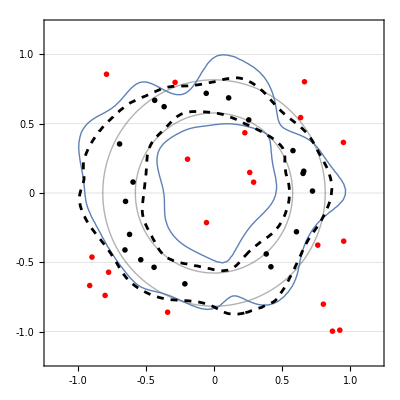

#Runs=2__#Traindata=40__#Testdata=8__r=0.6__ϕ=π/20__tre=0.5__Factor=1__#β'=c β,  c=1

General::munfl: Exp[-714.432] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

#SV=27

#SV=27

<AGT>=0.6875+-0.0883883<AST>=0.875+-0.

<AFT>=0.875+-0.

-Graphics3D-

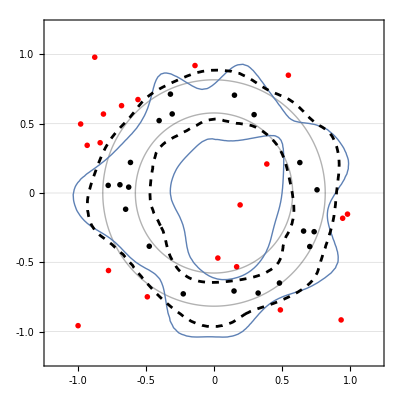

```mathematica
JJ=2;Np=10;Npt=2;rr=0.6;ϕ=Pi/20;
β=20.;c=1;Fa=1;tre=0.5; Print["#Runs=",JJ,"__","#Traindata=",4 Np,"__","#Testdata=",4 Npt,"__","r=",rr,"__","ϕ=",ϕ,"__","tre=",tre,"__","Factor=",Fa,"__","#β'=c β,  c=",c];
Kr[u_,v_,r_,φ_,β_]:=Exp[-β ⅇ^(2r)(Cos[ArcTan[v[[2]]/v[[1]]]+φ]u[[1]]+Sin[ArcTan[v[[2]]/v[[1]]]+φ]u[[2]]-(Cos[ArcTan[v[[2]]/v[[1]]]+φ]v[[1]]+Sin[ArcTan[v[[2]]/v[[1]]]+φ]v[[2]]))^2-β ⅇ^(-2r)(-Sin[ArcTan[v[[2]]/v[[1]]]+φ]u[[1]]+Cos[ArcTan[v[[2]]/v[[1]]]+φ]u[[2]]-(-Sin[ArcTan[v[[2]]/v[[1]]]+φ]v[[1]]+Cos[ArcTan[v[[2]]/v[[1]]]+φ]v[[2]]))^2];KoA[U_List,V_List,y_List,r_,φ_,β_,m_,Np_]:=1/(2Np)^2∑_(j=1)^(4Np) ∑_(i=1)^(4Np) ((-Abs[(m-y[[i]])])/2+1)((-Abs[(m-y[[j]])])/2+1)Kr[U[[i]],V[[j]],r,φ,β]
KoB[U_List,V_List,y_List,r_,φ_,β_,Np_]:=1/(2Np)^2∑_(j=1)^(4Np) ∑_(i=1)^(4Np) ((1-y[[i]] y[[j]])/2)Kr[U[[i]],V[[j]],r,φ,β];HS[U_List,V_List,y_List,r_,φ_,β_,Np_]:=KoA[U,V,y,r,φ,β,1,Np]+KoA[U,V,y,r,φ,β,-1,Np]-2 KoB[U,V,y,r,φ,β,Np];Fid[U_List,V_List,y_List,r_,φ_,β_,Np_]:=1/(2Np)∑_(j=1)^(4Np) ((-Abs[(1-y[[j]])])/2+1)Kr[U,V[[j]],r,φ,β]-1/(2 Np)∑_(j=1)^(4Np) ((-Abs[(-1-y[[j]])])/2+1)Kr[U,V[[j]],r,φ,β];
Do[h=0.6+0.1 la;acg=0;acn=0;
acgt=0;acnt=0;
AG={};AGT={};AC={};ACT={};
AFT={};Fha={};Rha={};Do[xym={};xym1={};xym2={};zm={};oo=1;ko=0;koo=2 Np;Subscript[aa, 1]={};Subscript[aa, 2]={};Do[
r={RandomReal[{-oo,oo}],RandomReal[{-oo,oo}]};If[Norm[r]<oo/√3-ko || Norm[r]>oo/√1.5,
If[Dimensions[Subscript[aa, 1]][[1]]<koo,Subscript[aa, 1]=Join[Subscript[aa, 1],{r}];xym=Join[xym,{r}];zm=Append[zm,1]]];If[oo/√1.5>Norm[r]>oo/√3+ko,If[Dimensions[Subscript[aa, 2]][[1]]< koo,Subscript[aa, 2]=Join[Subscript[aa, 2],{r}];xym=Join[xym,{r}];zm=Append[zm,-1]]];If[Dimensions[Subscript[aa, 1]][[1]]==koo,If[Dimensions[Subscript[aa, 2]][[1]]== koo,Goto[ei]]],{j,1,2000}];Label[ei];xym1=Subscript[aa, 1];xym2=Subscript[aa, 2];
ab1={};Do[Do[hj1=-5 Pi/40+j1 Pi/40;hjj1=jj1  0.05+0.45;ab1=Append[ab1,{hj1,hjj1, HS[xym,xym,zm,hjj1,hj1,β,Np]}],{j1,0,10}],{jj1,0,10}];Bb1={};Do[Bb1=Append[Bb1,ab1[[iu,3]]],{iu,1,11 11}];Fb1=Max[Bb1];fs1=Position[Bb1,Fb1];dar1=ab1[[fs1[[1,1]]]];rr=dar1[[2]];ϕ=dar1[[1]];Fha=Append[Fha,ϕ];Rha=Append[Rha,rr];
gg=ListPlot[{xym1,xym2}];
xymt={};xym1t={};xym2t={};zmt={};oo=1;ko=0;koo=2 Npt;Subscript[aa, 1]={};Subscript[aa, 2]={};Do[
r={RandomReal[{-oo,oo}],RandomReal[{-oo,oo}]};If[Norm[r]<oo/√3-ko || Norm[r]>oo/√1.5,
If[Dimensions[Subscript[aa, 1]][[1]]<koo,Subscript[aa, 1]=Join[Subscript[aa, 1],{r}];xymt=Join[xymt,{r}];zmt=Append[zmt,1]]];If[oo/√1.5>Norm[r]>oo/√3+ko,If[Dimensions[Subscript[aa, 2]][[1]]< koo,Subscript[aa, 2]=Join[Subscript[aa, 2],{r}];xymt=Join[xymt,{r}];zmt=Append[zmt,-1]]];If[Dimensions[Subscript[aa, 1]][[1]]==koo,If[Dimensions[Subscript[aa, 2]][[1]]== koo,Goto[ei]]],{j,1,2000}];Label[ei];xym1t=Subscript[aa, 1];xym2t=Subscript[aa, 2];
Do[da=ii-0.5;If[da>-2,K[u_,v_]:=Exp[-β (u-v).(u-v)];SupportVectorClassifier[xm_,ym_,K_,c_]:=Module[{m,n,M,i,j,W,g,vars,sol,bdata,b},m=Length[ym];n=Length[xm[[1]]];
M=Table[K[xm[[i]],xm[[j]]],{i,1,m},{j,1,m}]+(1/c) IdentityMatrix[m];
W=∑_(i=1)^m Subscript[α, i]- 0.5 ∑_(i=1)^m ∑_(j=1)^m (Subscript[α, i] Subscript[α, j] ym[[i]] ym[[j]] M[[i,j]]);
g=Apply[And,Join[Table[Subscript[α, i]≥0,{i,1,m}],{∑_(i=1)^m Subscript[α, i] ym[[i]]==0}]];
vars=Table[Subscript[α, i],{i,1,m}];
sol=NMaximize[{W,g},vars][[2]];
bdata=Table[((1-Subscript[α, j]/c)/ym[[j]]-∑_(i=1)^m (ym[[i]] Subscript[α, i] K[xm[[i]],xm[[j]]]))/.sol[[2]],{j,1,m}];
b=Apply[Plus,bdata]/m;If[da<0,{((∑_(i=1)^m (ym[[i]] Subscript[α, i] K[Table[Subscript[x, j],{j,1,n}],xm[[i]]]))+b)
/.sol,vars/.sol},{((∑_(i=1)^m (ym[[i]] Subscript[α, i] K[Table[Subscript[x, j],{j,1,n}],xm[[i]]]))+b)
/.sol,vars/.sol}]];SV=SupportVectorClassifier[xym,zm,K,5];KK=Dimensions[xym][[1]];xsv={};asv={};Do[If[SV[[2,i]]>tre,xsv=Append[xsv,xym[[i]]];asv=Append[asv,SV[[2,i]]]],{i,1,KK}];ASV=Max[asv];mm=Dimensions[asv][[1]];If[jj==1,Print["#SV=",mm]];
F[x1_,x2_]:=SV[[1]]/.{Subscript[x, 1]->x1,Subscript[x, 2]-> x2 }];
(***********)
If[da>0,K[u_,v_]:=Kr[u,v,rr,ϕ,c β];SupportVectorClassifier[xm_,ym_,K_,c_]:=Module[{m,n,M,i,j,W,g,vars,sol,bdata,b},m=Length[ym];n=Length[xm[[1]]];
M=Table[K[xm[[i]],xm[[j]]],{i,1,m},{j,1,m}]+(1/c) IdentityMatrix[m];
W=∑_(i=1)^m Subscript[α, i]- 0.5 ∑_(i=1)^m ∑_(j=1)^m (Subscript[α, i] Subscript[α, j] ym[[i]] ym[[j]] M[[i,j]]);
g=Apply[And,Join[Table[Subscript[α, i]≥0,{i,1,m}],{∑_(i=1)^m Subscript[α, i] ym[[i]]==0}]];
vars=Table[Subscript[α, i],{i,1,m}];
sol=NMaximize[{W,g},vars][[2]];
bdata=Table[((1-Subscript[α, j]/c)/ym[[j]]-∑_(i=1)^m (ym[[i]] Subscript[α, i] K[xm[[i]],xm[[j]]]))/.sol[[2]],{j,1,m}];
b=Apply[Plus,bdata]/m;If[da<0,{((∑_(i=1)^m (ym[[i]] Subscript[α, i] K[Table[Subscript[x, j],{j,1,n}],xm[[i]]]))+b)
/.sol,vars/.sol},{((∑_(i=1)^m (ym[[i]] Subscript[α, i] K[Table[Subscript[x, j],{j,1,n}],xm[[i]]]))+b)
/.sol,vars/.sol}]];SV=SupportVectorClassifier[xym,zm,K,5];F[x1_,x2_]:=SV[[1]]/.{Subscript[x, 1]->x1,Subscript[x, 2]-> x2 }];

(***********)Accu[xym_,zm_,i_]:=Sign[F[xym[[i,1]],xym[[i,2]]] zm[[i]]];go=0;Do[If[Accu[xymt,zmt,j]>0,go=go+1],{j,1,4 Npt}]; If[da<0,acgt=acgt+N[go/(4 Npt)];AGT=Append[AGT,N[go/(4 Npt)]],acnt=acnt+N[go/(4 Npt)];ACT=Append[ACT,N[go/(4 Npt)]]];
go=0;Do[If[Accu[xym,zm,j]>0,go=go+1],{j,1,4 Np}];If[da<0,acg=acg+N[go/(4 Np)];AG=Append[AG,N[go/(4 Np)]],acn=acn+N[go/(4 Np)];AC=Append[AC,N[go/(4 Np)]]];
If[da>0,
Accu2[xym_,zm_,xymm_,zmm_,i_]:=Sign[Fid[xym[[i]],xymm,zmm,rr,ϕ,β,Np] zm[[i]]];
go=0;Do[If[Accu2[xymt,zmt,xym,zm,j]>0,go=go+1],{j,1,4 Npt}]; AFT=Append[AFT,N[go/(4 Npt)]]];

If[jj==JJ,If[da<0,If[jj==JJ,Subscript[SS, ii]=ContourPlot[F[x1,x2]==0,{x1,-2,2.2},{x2,-2,2.2},ContourStyle->Thick]],If[jj==JJ,Subscript[SS, ii]=ContourPlot[F[x1,x2]==0,{x1,-2,2.2},{x2,-2,2.2},ContourStyle->Directive[Black,Dashed]]]];If[da<0,If[jj==JJ,Subscript[S, ii]=Plot3D[F[x1,x2],{x1,-1.5,1.5},{x2,-1.5,1.5},PlotRange->All,PlotStyle->Red]],If[jj==JJ,Subscript[S, ii]=Plot3D[F[x1,x2],{x1,-1.5,1.5},{x2,-1.5,1.5},PlotRange->All,PlotStyle->Blue]](*If[jj==JJ,Subscript[S, ii]=ContourPlot[F[x1,x2]==0,{x1,-2,2.2},{x2,-2,2.2},ContourStyle->Thick]],If[jj==JJ,Subscript[S, ii]=ContourPlot[F[x1,x2]==0,{x1,-2,2.2},{x2,-2,2.2},ContourStyle->Directive[Black,Dashed]]]*)]],{ii,0,1}],{jj,1,JJ}];(*Print["<AG>=",acg/JJ,"+-",StandardDeviation[AG],"<AS>=",acn/JJ,"+-",StandardDeviation[AC]];*)Print["<AGT>=",acgt/JJ,"+-",StandardDeviation[AGT],"<AST>=",acnt/JJ,"+-",StandardDeviation[ACT]];Print["<AFT>=",Mean[AFT],"+-",StandardDeviation[AFT]];Print[Show[Subscript[S, 0],Subscript[S, 1],PlotRange->{{-1,2.2},{-1,2.2}}]];
gg=ListPlot[{xym1,xym2},PlotRange->{{-1.2,1.2},{-1.2,1.2}},PlotStyle->{Directive[Red,PointSize[Large]],Directive[Black,PointSize[Large]]},PlotTheme->"Business",AspectRatio->1];a=ParametricPlot[{1/√1.5{Sin[t],Cos[t]},1/√3{Sin[t],Cos[t]}},{t,0,2Pi},PlotRange->{-1.2,1.2},PlotStyle->Directive[Black,Thick,Opacity[0.3]],AspectRatio->1];Print[Show[gg,a,Subscript[SS, 0],Subscript[SS, 1]]],{la,0,0}];
```

```mathematica
Fha
```

{-π/8,-π/20}

```mathematica
Rha
```

{0.95,0.65}